# Non-Unitary Dynamics of Quantum States

Here, we gives a illustration how non-unitary dynamics of quantum states arise from the interaction of the system with its environment.

Make sure that the Q3 package is loaded to use the demonstrations in this documentation.

```mathematica
<<Q3`
```

Throughout this document, symbol S will be used to denote qubits and Pauli operators on them.

```mathematica
Let[Qubit,S]
```

Let us consider a total system consisting of two qubits, one representing the “system” and the other the “environment”.

```mathematica
SS=S[{1,2},None]
```

{S_1,S_2}

Initially, the total system is assumed to be in a product state.

```mathematica
in=Ket[];
LogicalForm[in,SS]
```

0_S_10_S_2

Suppose that we want to perform a single-qubit rotation around the x-axis. The required Hamiltonian of the system involves the Pauli-X operator.

```mathematica
H0=S[1,1]*Ω/2;
H0//PauliForm
```

(X Ω)/2

We choose Ω as our basic energy scale to measure all other energies  and time.

```mathematica
Ω=1
```

1

Unfortunately, the system is coupled to the environment via the Ising-type YY interaction. Here, J is the coupling constant.

```mathematica
Hint=J/2*S[1,2]**S[2,2];
Hint//PauliForm
Let[Real,J]
```

(J Y⊗Y)/2

This the total Hamiltonian of the total system.

```mathematica
HH=H0+Hint;
HH//PauliForm
```

(X⊗I)/2+(J Y⊗Y)/2

The evolution of the total system as a closed system is governed by this time-evolution operator.

```mathematica
U[t_]=MultiplyExp[-I*t*HH]//Elaborate;
U[t]//PauliForm
Let[Real,t]
```

1/2 ⅇ^(-1/2 ⅈ √(1+J^2) t) (1+ⅇ^(ⅈ √(1+J^2) t)) I⊗I-(ⅇ^(-1/2 ⅈ √(1+J^2) t) (-1+ⅇ^(ⅈ √(1+J^2) t)) X⊗I)/(2 √(1+J^2))-(ⅇ^(-1/2 ⅈ √(1+J^2) t) (-1+ⅇ^(ⅈ √(1+J^2) t)) J Y⊗Y)/(2 √(1+J^2))

The above expression looks simpler with the trigonometric functions than the exponential function.

```mathematica
U[t_]=MultiplyExp[-I*t*HH]//Elaborate//ExpToTrig;
U[t]//PauliForm
```

-(X⊗I (Cos[1/2 √(1+J^2) t]-ⅈ Sin[1/2 √(1+J^2) t]) (-1+Cos[√(1+J^2) t]+ⅈ Sin[√(1+J^2) t]))/(2 √(1+J^2))-(J Y⊗Y (Cos[1/2 √(1+J^2) t]-ⅈ Sin[1/2 √(1+J^2) t]) (-1+Cos[√(1+J^2) t]+ⅈ Sin[√(1+J^2) t]))/(2 √(1+J^2))+1/2 I⊗I (Cos[1/2 √(1+J^2) t]-ⅈ Sin[1/2 √(1+J^2) t]) (1+Cos[√(1+J^2) t]+ⅈ Sin[√(1+J^2) t])

Here is the final state of the total system.

```mathematica
out=U[t]**in;
out//LogicalForm
```

Cos[1/2 √(1+J^2) t] 0_S_10_S_2-(ⅈ 1_S_10_S_2 Sin[1/2 √(1+J^2) t])/(√(1+J^2))+(ⅈ J 1_S_11_S_2 Sin[1/2 √(1+J^2) t])/(√(1+J^2))

Note that the above state has entanglement between the system and environment. To see this, the environment is traced out. After all, we have no access to the environment.

```mathematica
rho=PartialTrace[out,SS,S[2]]//Elaborate
Matrix[rho,S[1]]//MatrixForm
```

1/2+1/2 Cos[√(1+J^2) t] S_1^z-(S_1^y Sin[√(1+J^2) t])/(2 √(1+J^2))

(1/2+1/2 Cos[√(1+J^2) t] | (ⅈ Sin[√(1+J^2) t])/(2 √(1+J^2))
-(ⅈ Sin[√(1+J^2) t])/(2 √(1+J^2)) | 1/2-1/2 Cos[√(1+J^2) t])

The degree of entanglement between the system and environment in state out can be quantified by the von Neumann entanglement of reduced density operator rho.

```mathematica
entropy[t_]=VonNeumannEntropy[PartialTrace[out,S[2]]]
```

-((2 √(1+J^2)-√2 √(2+J^2+J^2 Cos[2 √(1+J^2) t])) Log[(2 √(1+J^2)-√2 √(2+J^2+J^2 Cos[2 √(1+J^2) t]))/(4 √(1+J^2))])/(4 √(1+J^2) Log[2])-((2 √(1+J^2)+√2 √(2+J^2+J^2 Cos[2 √(1+J^2) t])) Log[(2 √(1+J^2)+√2 √(2+J^2+J^2 Cos[2 √(1+J^2) t]))/(4 √(1+J^2))])/(4 √(1+J^2) Log[2])

Plot the entropy as a function of time.

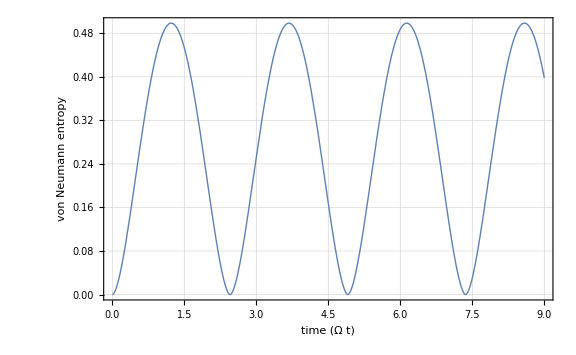

```mathematica
Block[
{J=0.8},
Plot[Chop@entropy[t],{t,0,9},
PlotRange->All,
FrameLabel->{"time (Ω t)","von Neumann entropy"}]
]
```